# Unidad 1 1 - Álgebra y gráficas

## Conceptos básicos

En Mathematica existen dos tipo de entrada: Código y texto. El código se puede ejecutar con Shift+Enter.

```mathematica
5
```

5

```mathematica
5^2
```

25

```mathematica
5^2
```

25

Se pueden guardar datos en variables.

```mathematica
x = 6
```

6

Para ocultar el resultado de la asignación escribimos punto y coma al final del statement.

```mathematica
x = 6;
```

Se pueden hacer operaciones con las variables definidas

```mathematica
x+1
```

7

Por ejemplo la raíz cuadrada de x

```mathematica
√x
```

√6

Mathematica deja la expresión en forma simbólica, no la evalúa. Para forzarlo a que realice la evaluación se hace

```mathematica
N[√x]
```

2.44949

Podemos especificarle el número de decimales que queremos

```mathematica
N[√x,20]
```

2.4494897427831780982

En Mathematica hay muchas funciones predefinidas, como Sin, Cos, Tan, Log, N, Plot, etc...

```mathematica
Sin[5]
```

Sin[5]

```mathematica
N[Sin[5]]
```

-0.958924

Se pueden manipular expresiones algebraicas.
Para simplificar

```mathematica
Clear[x]
```

```mathematica
expresion = (x^2+1)x+6x
```

6 x+x (1+x^2)

```mathematica
FullSimplify[expresion]
```

x (7+x^2)

Para expandir

```mathematica
Expand[expresion]
```

7 x+x^3

También se pueden resolver ecuaciones algebraicas. Solve las resuelve de manera simbólica.

```mathematica
Solve[x== 7x+9,x]
```

{{x→-3/2}}

```mathematica
Solve[Sin[x]==0.8,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.927295}}

Algunas veces la manera simbólica de resolver ecuaciones no es la más eficiente,

```mathematica
Solve[Cos[x]==x,x,Reals]
```

{{x→Root[{-Cos[#1]+#1&,0.73908513321516064166}]}}

es por eso que existe la opción de resolver la ecuación numéricamente.

```mathematica
NSolve[Cos[x]==x,x,Reals]
```

{{x→0.739085}}

Para resolver ecuaciones simultáneas se hace

```mathematica
Solve[{x+y==7,4x-5y == 2},{x,y}]
```

{{x→37/9,y→26/9}}

Ejercicio

Resolver el sistema de ecuaciones
Cos(x+y) = x,
y = x+2

## Gráficas simples

La función Plot nos permite realizar gráficas de expresiones algebraicas

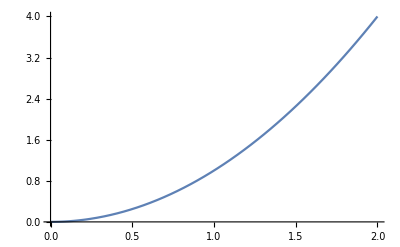

```mathematica
Plot[x^2,{x,0,2}]
```

El aspecto por defecto de la gráfica es muy simple, pero existen muchas opciones para personalizarla

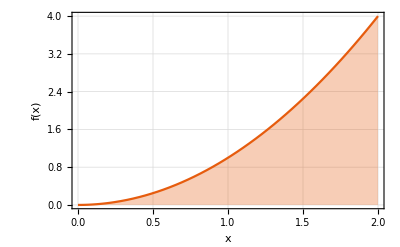

```mathematica
Plot[x^2,{x,0,2},PlotTheme->"Scientific", FrameLabel->{"x","f(x)"},ImageSize->400,BaseStyle->FontSize->16,GridLines->Automatic,Filling->Bottom]
```

Se pueden agrupar varias gráficas

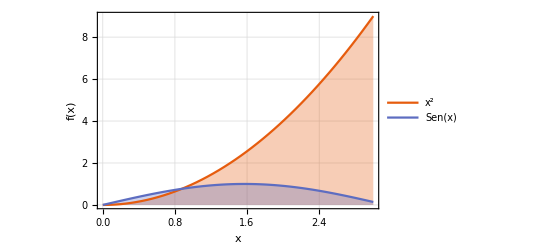

```mathematica
Plot[{x^2,Sin[x]},{x,0,3},PlotTheme->"Scientific", FrameLabel->{"x","f(x)"},ImageSize->400,BaseStyle->FontSize->16,GridLines->Automatic,Filling->Bottom,PlotLegends->{"x^2","Sen(x)"}]
```

Existen más tipos de gráficas que se pueden realizar, como gráficas en 3d

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},PlotTheme->"Scientific", AxesLabel->{"x","y","z"},BaseStyle->FontSize->16]
```

-Graphics3D-

Se pueden realizar gráficas implícitas. Nótese que la intersección coincide con la solución.

{{x→4.11111,y→2.88889}}

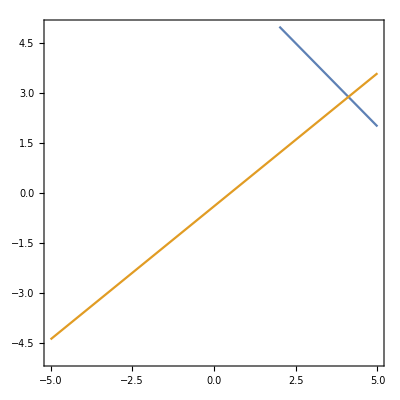

```mathematica
N[Solve[{x+y==7,4x-5y == 2},{x,y}]]
ContourPlot[{x+y==7,4x-5y == 2},{x,-5,5},{y,-5,5}]
```

Ejercicio

Graficar
Cos(x+y) = x,
y = x+2
y comprobar que la intersección coincide con la solución del sistema de ecuaciones.

## Elementos interactivos

Agregando un Manipulate se puede hacer interactivo cualquier tipo de elemento

```mathematica
Manipulate[
Plot[{x^2,Sin[a x]},{x,0,3},PlotTheme->"Scientific", FrameLabel->{"x","f(x)"},ImageSize->400,BaseStyle->FontSize->16,GridLines->Automatic,Filling->Bottom,PlotLegends->{"x^2","Sen(ax)"}],
{a,1,5}
]
```

Se pueden combinar gráficas para hacer efectos

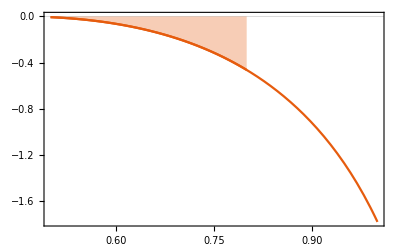

```mathematica
Show[
Plot[Log[Sin[Exp[x]]^2],{x,0.5,1},PlotTheme->"Scientific"],
Plot[Log[Sin[Exp[x]]^2],{x,0.5,0.8},Filling->Top,PlotTheme->"Scientific"]
]
```

Ejercicio

Crear un elemento interactivo que encuentre la solución de
Cos(x+y) = ax,
y = x+2,
donde a es un elemento variable de 1 a 2.

```mathematica
Manipulate[Quiet[NSolve[{Cos[x+y] == x,y ==  x+2a},{x,y},Reals]],{a,1,2}]
```

## Derivadas e integrales

Mathematica puede hacer operaciones de cálculo de manera simbólica, por ejemplo derivadas

```mathematica
D[x^7,x]
```

7 x^6

```mathematica
D[Log[Sin[Exp[x]]^2],x]
```

2 ⅇ^x Cot[ⅇ^x]

Para evaluar la derivada en algún punto se puede usar una regla de sustitución

```mathematica
N[D[Log[Sin[Exp[x]]^2],x] /. {x->8}]
```

-13589.1

De manera análoga se pueden realizar integrales

```mathematica
Integrate[7 x^6,x]
```

x^7

```mathematica
Integrate[Log[Sin[Exp[x]]^2],x]
```

-2 (-∫Log[Sin[ⅇ^x]]ⅆx+x Log[Sin[ⅇ^x]])+x Log[Sin[ⅇ^x]^2]

Se puede evaluar la integral en un intervalo. Por defecto Mathematica trata de hacerlo de manera simbólica

```mathematica
Integrate[7 x^6,{x,5,6}]
```

201811

Sin embargo no siempre tiene éxito.

```mathematica
Integrate[Log[Sin[Exp[x]]^2],{x,0.5,1}]
```

∫_0.5^1 Log[Sin[ⅇ^x]^2]ⅆx

En éstos casos es necesario realizar la integral numéricamente.

```mathematica
NIntegrate[Log[Sin[Exp[x]]^2],{x,0.5,1}]
```

-0.244913

Ejercicio

Hacer un elemento interactivo que muestre el resultado de la integración numérica de Log((Sin(Exp(x)))^2) de 0.5 a “a”, donde “a” es un elemento variable. Luego crear una gráfica que muestre en sombreado el área que se está integrando.

```mathematica
Manipulate[
Column[{
NIntegrate[Log[Sin[Exp[x]]^2],{x,0.5,a}],
Show[
Plot[Log[Sin[Exp[x]]^2],{x,0.5,1},PlotTheme->"Scientific",ImageSize->500],
Plot[Log[Sin[Exp[x]]^2],{x,0.5,a},Filling->Top,PlotTheme->"Scientific",ImageSize->500]
]}
],
{{a,0.6},0.5001,1}
]
```

## Listas

En Mathematica se puede trabajar con listas también. La síntaxis es

```mathematica
a = {1,3,7,9,3,3};
```

Los elementos de la lista se pueden graficar

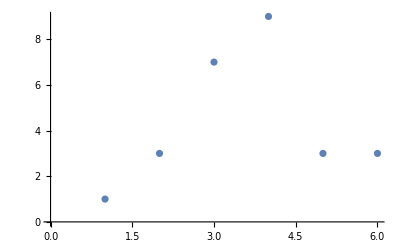

```mathematica
ListPlot[a]
```

Y se puede acceder a ellos de diferentes maneras. Para acceder al elemento 4, por ejemplo

```mathematica
a[[4]]
```

9

Para acceder a los elementos del 2 a al 5

```mathematica
a[[2;;5]]
```

{3,7,9,3}

También se puede acceder a los elementos “hacia atrás”

```mathematica
a[[-1]]
```

3

En la gráfica que hice anteriormente sólo se graficó el valor de cada entrada, poniendo el índice de la entrada en el eje x y el valor de la lista en el eje y. Para especificar el valor de x y y se puede hacer una lista de listas.

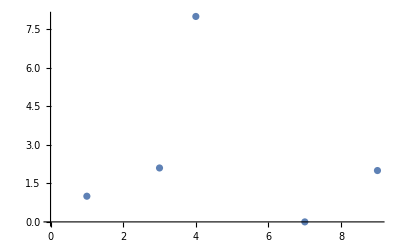

```mathematica
a = {{1,1},{3,2.1},{9,2},{4,8},{7,0}};
ListPlot[a]
```

Se puede automatizar el proceso de crear listas para no tener que introducir manualmente cada uno de sus elementos. Para eso usamos las tablas.

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

La sintaxis de las tablas es muy flexible, por ejemplo se puede hacer una tabla para evaluar los valores de una función

```mathematica
sin = Table[{x,Sin[x]},{x,0,2 π,0.001}]
```

{{0.,0.},{0.001,0.001},{0.002,0.002},{0.003,0.003},{0.004,0.00399999},{0.005,0.00499998},{0.006,0.00599996},{0.007,0.00699994},{0.008,0.00799991},{0.009,0.00899988},6265,{6.275,-0.00818522},{6.276,-0.00718525},{6.277,-0.00618527},{6.278,-0.00518528},{6.279,-0.00418529},{6.28,-0.0031853},{6.281,-0.00218531},{6.282,-0.00118531},{6.283,-0.000185307}}
 |  |  |  |

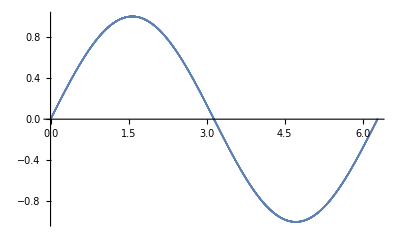

```mathematica
ListPlot[sin]
```